```mathematica
ClearAll["Global`*"]
nd=NotebookDirectory[];

(*Constants of nature*)
ℒsun=3.839×10^33;
c=2.99792458×10^10;
h=6.626068×10^-27;
kb=1.3806503×10^-16;
eV=1.60217646×10^-12;

(*Load various lit data*)
pdata=Import[nd<>"paumard-2006.txt","TSV"];
pdata⟦All,1⟧=(StringSplit[#,{":",","}]&)/@(pdata⟦All,1⟧);
hdata=Import[nd<>"habibi-2017.txt","TSV"];
gdata=Import[nd<>"gillessen-2016.txt","Table"];
gdata=gdata⟦Range[1,Length@gdata-5]~Join~Range[Length@gdata-3,Length@gdata]⟧;
gdata=Select[gdata,#⟦-3⟧=="e"&];
{as,es,is,ωs,Ωs,Tps,Ps}=gdata⟦All,{2,4,6,10,8,12,14}⟧ᵀ;

(*Eulerian coordinates to Cartesian*)
cart:={r(Cos[ω+ν]Cos[Ω]-Sin[ω+ν]Sin[Ω]Cos[i]),
r(Cos[ω+ν]Sin[Ω]+Sin[ω+ν]Cos[Ω]Cos[i]),
r Sin[ω+ν]Sin[i]+.001};
Ε[M_,e_]=Nest[Kepler,M,5];
Εf=Ε[M,e];
Εff[MM_,ee_]:=N[Εf/.{M->MM,e->ee}];
Kepler[Ε_]:=M+e Sin[Ε];
$Elliptic:={r Cos[ν]:>a(Cos[Ε]-e),r Sin[ν]:>a √(1-e^2)Sin[Ε],t-t0:> 1/n(Ε-e Sin[Ε]),Ε->Kepler[]};
XYZ=Function[{a,e,i,ω,Ω,Ε},TrigExpand[cart]/.$Elliptic//Evaluate];
Geometry[{a_,e_,i_,ω_,Ω_,M_},opts___]:=
{Line[
{{XYZ[a,e,i,ω,Ω,0],XYZ[a,e,i,ω,Ω,180°]}(*a*),
{XYZ[a,e,i,ω,Ω,90°],XYZ[a,e,i,ω,Ω,270°]}(*b*),
{XYZ[a,e,i,ω,Ω,0°],XYZ[a,e,i,ω,Ω,90°]}}]};
```

```mathematica
(*Ionizing radiation fraction*)
ℐfrac[𝒯_,νmin_:(13.6eV/h)]:=(2 h)/c^2 NIntegrate[SetPrecision[ν^3/(Exp[h ν/(kb 𝒯)]-1),20],{ν,νmin,∞},MaxRecursion->15,WorkingPrecision->20]((2 π^4 kb^4)/(15 h^3 c^2)𝒯^4)^-1;
tempsubs=Table[hdata⟦p,1⟧->hdata⟦p,2⟧,{p,Length@hdata}];
lumsubs=Table[hdata⟦p,1⟧->ℒsun 10^hdata⟦p,8⟧,{p,Length@hdata}];
blumsubs=Table[gdata⟦g,1⟧->(ℒsun 10^hdata⟦-1,8⟧10^((gdata⟦7,-2⟧-gdata⟦All,-2⟧)/2.5))⟦g⟧,{g,Length@gdata}];
(*
Here we use the data in Habibi (if available), otherwise we use the dimmest star in Habibi and scale the luminosity based on the difference in K-band magnitude.
*)
slums=gdata⟦All,1⟧/.lumsubs;
slums=slums/.blumsubs;
temps=gdata⟦All,1⟧/.tempsubs;
temps=temps/.Table[gdata⟦g,1⟧->temps⟦7⟧,{g,Length@gdata}];
ℐlum=slums(ℐfrac/@temps);
ℐlum/=Max@ℐlum;
```

```mathematica
Ms=(Tps-tnow)/Ps 2π;
Es=Εff[#⟦1⟧,#⟦2⟧]&/@({Ms,es}ᵀ);
coords=XYZ@@#&/@({as,es,is,ωs,Ωs,Es}ᵀ);
coords*=(2π/360/3600)*8000*1191.29;   
(*Manipulate[coords⟦1⟧/.tnow->tn,{tn,2010,2030}]*)
Manipulate[ListPointPlot3D[coords/.tnow->tn,PlotRange->50*{{-1,1},{-1,1},{-1,1}},BoxRatios->1],{tn,2010,2030}]
```

ListPointPlot3D::arrayerr: coords must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

```mathematica
Clear[interactivePlots]
```

```mathematica
radius=2boxsize;
conebase=radius Tan[90°-openingAngle];
myregion=RegionDifference[RegionDifference[Ball[{0,0,0},radius],Cone[{{0,0,radius},{0,0,0}},conebase]],Cone[{{0,0,-radius},{0,0,0}},conebase]];
test=RandomPoint[myregion,10000];
ListPointPlot3D[test,BoxRatios->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
(* Make the distribution of line-emitting gas, distance units = light days *)
(* Set parameter values: *)
boxsize=5;
nclouds=500;
rmin =10;  (* minimum radius of emitting gas *)
rmean = 40;  (* mean radius of emitting gas *)
(*radialShape =0.2;   --> 0.1 is a Gaussian, 1 = exponential, > 1 is steeper than exponential *)
inclination = 30°;  (* units of deg, 0 deg is face-on, 90 deg is edge-on *)
(*openingAngle = 80°;   units of deg, 0 deg is thin disk, 90 deg is sphere *)
(* Calculate gas distribution: *)
alpha = 1/radialShape^2;
beta = (rmean - rmin)*radialShape^2;

interactivePlots[tn_?NumericQ,rs_?NumericQ,oa_?NumericQ]:=Module[{radius,conebase,myregion,vels,clouds,losvel,intensities,vec},
radius=2boxsize;
conebase=N[radius Tan[90°-oa]];
myregion=RegionDifference[RegionDifference[Ball[{0,0,0},radius],Cone[{{0,0,radius},{0,0,0}},conebase]],Cone[{{0,0,-radius},{0,0,0}},conebase]];
clouds=(rmin + RandomVariate[GammaDistribution[alpha,beta]/.radialShape->rs,nclouds])*Normalize/@RandomPoint[myregion,nclouds];
vels=1/(Norm/@clouds)^(3/2)(RotationTransform[90°][#⟦;;2⟧]&/@clouds);
losvel={1,0}.#&/@vels;
intensities=Total[Table[ℐlum⟦s⟧/Norm[clouds⟦c⟧-coords⟦s⟧]^2,{c,Length@clouds},{s,Length@coords}],{2}];
vec={losvel,intensities}ᵀ;
vec=Sort[vec,#1⟦1⟧<#2⟦1⟧&];

Grid[{
{Show[ListPointPlot3D[clouds,PlotStyle->{Directive[PointSize@0.015,Blue]}],Graphics3D[{Orange,Sphere[#,2]}&/@(coords/.tnow->tn)],PlotRange->50*{{-1,1},{-1,1},{-1,1}},BoxRatios->1,ImageSize->500,AspectRatio->1],ListPlot[{losvel,intensities}ᵀ/. {tnow-> tn},ImageSize->500,AspectRatio->1]},
{Histogram[WeightedData[vec⟦All,1⟧,vec⟦All,2⟧]/. {tnow-> tn},10,PlotRange->{Automatic,{0,0.02 nclouds/100}},ImageSize->500,AspectRatio->1]}},ItemSize->All]
]
```

```mathematica
Manipulate[interactivePlots[tn,rs,oa],{tn,1990,2030},{rs,0.1,1.5},{oa,N[1°],N[89°]},ContinuousAction->False]
```

hi

hola

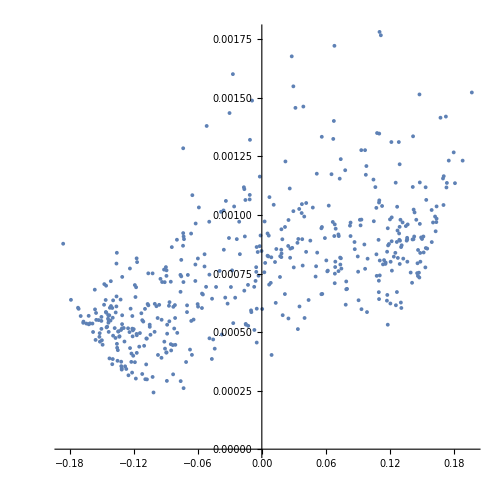
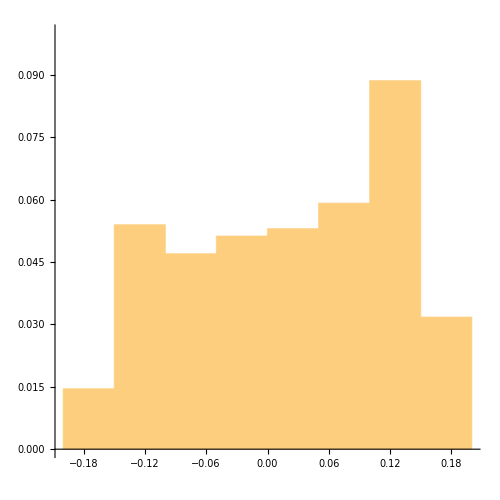
-Graphics3D- | -Graphics-
-Graphics- |

```mathematica
interactivePlots[2020,0.3,45°]
```

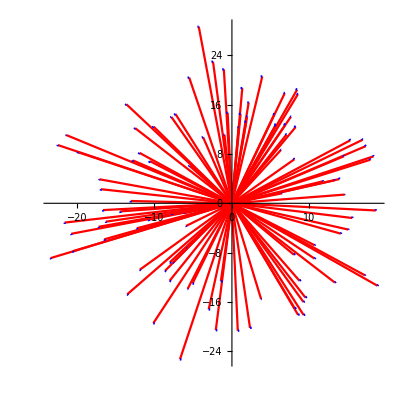

```mathematica
l1=ListPlot[{{0,0},#}&/@clouds⟦All,;;2⟧,Joined->True,PlotStyle->Red];
l2=ListPlot[Table[{clouds⟦i⟧⟦;;2⟧,clouds⟦i⟧⟦;;2⟧+vels⟦i⟧},{i,Length@clouds}],Joined->True,PlotStyle->Blue];
Show[l1,l2,AspectRatio->1]
```

```mathematica
(* A repository of code that works for Anna to use as examples when coding *)
(*nstars=10;
stars={{0,0,0}}~Join~RandomPoint[Ball[{0,0,0},2*boxsize],nstars];*)
(*clouds=4/5 RandomVariate[GammaDistribution[1/0.2^2,1],nclouds]*Normalize/@RandomPoint[Ball[{0,0,0},2*boxsize],nclouds];
vels=1/(Norm/@clouds)^(3/2)(RotationTransform[90°][#⟦;;2⟧]&/@clouds);
losvel={1,0}.#&/@vels;
intensities=Total[Table[ℐlum⟦s⟧/Norm[clouds⟦c⟧-coords⟦s⟧]^2,{c,Length@clouds},{s,Length@coords}],{2}];
Manipulate[ListPlot[{losvel,intensities}ᵀ/. tnow-> tn ],{tn,1990,2030},ContinuousAction->False]
vec={losvel,intensities}ᵀ;
vec=Sort[vec,#1⟦1⟧<#2⟦1⟧&];
Manipulate[Histogram[WeightedData[vec⟦All,1⟧,vec⟦All,2⟧]/. tnow-> tn,PlotRange->{Automatic,{0,1}}],{tn,1990,2030},ContinuousAction->False]*)
```

```mathematica
(*Manipulate[ListPlot[{losvel,intensities}ᵀ/. {tnow-> tn, rmin -> rmi} ],{tn,1990,2030}, {rmi,1, 50},ContinuousAction->False]*)
```